## Single bar

### Governing equations

```mathematica
$Assumptions={λx>0, λ>0, γ>0, μ>0, κ>0, χ>0, l>0, L>0, l1>0, l2>0, L1>0, L2>0, Tex>0}
```

{λx>0,λ>0,γ>0,μ>0,κ>0,χ>0,l>0,L>0,l1>0,l2>0,L1>0,L2>0,Tex>0}

```mathematica
Aten=DiagonalMatrix[{α,α,αz}];
Gten=DiagonalMatrix[{1,1,γ}];
Bten=Aten.Transpose[Aten];
I1=Tr[Transpose[Aten].Aten];
Id=IdentityMatrix[3];
```

```mathematica
Tten=μ/Det[Aten](Bten-Id)+κ (Det[Aten]-1)Id;
subα=Solve[{Tten[[1,1]]==0,Tten[[3,3]]==fext/α^2} ,{α, αz}][[4]];
```

```mathematica
Tten[[1,1]]
```

(-1+α^2 αz) κ+((-1+α^2) μ)/(α^2 αz)

```mathematica
Tten[[3,3]]
```

(-1+α^2 αz) κ+((-1+αz^2) μ)/(α^2 αz)

```mathematica
Tten[[3,3]]/.subα/.{μ->1, κ->1, fext->-1}//N
```

-0.861397

```mathematica
subα/.{μ->1, κ->1, fext->-1}//N
```

{α→1.07745,αz→0.687815}

```mathematica
W=μ/2(I1-3-2Log[Det[Aten]])+κ/2(Det[Aten]-1)^2+χ/2((Det[Gten]-1)/(Det[Gten]+1))^2
RHS=ps+1(Det[Aten] fext/α^2-W)-(2 χ (-1+Det[Gten]) Det[Gten])/(1+Det[Gten])^3
```

1/2 (-1+α^2 αz)^2 κ+((-1+γ)^2 χ)/(2 (1+γ)^2)+1/2 μ (-3+2 α^2+αz^2-2 Log[α^2 αz])

ps+fext αz-1/2 (-1+α^2 αz)^2 κ-(2 (-1+γ) γ χ)/(1+γ)^3-((-1+γ)^2 χ)/(2 (1+γ)^2)-1/2 μ (-3+2 α^2+αz^2-2 Log[α^2 αz])

```mathematica
Coefficient[RHS, χ]//FullSimplify
```

-1/2-4/(1+γ)^3+4/(1+γ)^2

```mathematica
RHS-χ Coefficient[RHS, χ]//FullSimplify
```

ps+fext αz-1/2 (-1+α^2 αz)^2 κ-1/2 (-3+2 α^2+αz^2) μ+μ Log[α^2 αz]

### Long definitions

```mathematica
(* RHS/.subα *)
```

```mathematica
rhsFull[γ_, ps_, χ_, fext_,μ_, κ_ ]:=ps-(2 (-1+γ) γ χ)/(1+γ)^3-((-1+γ)^2 χ)/(2 (1+γ)^2)+1/(κ μ (fext^3-fext^2 μ-κ μ^2))fext (fext^4 κ-fext^3 κ μ-fext κ^2 μ^2+fext^2 μ^3+fext κ μ^3+κ μ^4+fext^3 κ μ Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]+fext^2 κ^2 μ Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]+fext^2 κ μ^2 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]+fext κ^2 μ^2 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]-fext^2 μ^3 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]-fext κ μ^3 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]-κ μ^4 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]-fext^4 κ Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^2-fext^3 κ^2 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^2+κ^3 μ^2 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^2+κ^2 μ^3 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^2-fext^3 κ^2 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^3-fext κ^3 μ Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^3-2 fext^2 κ μ^2 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^3-fext κ^2 μ^2 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^3-2 κ^2 μ^3 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^3-fext^2 κ^2 μ Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^4-fext^2 κ^2 μ Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^5-κ^3 μ^2 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^5)-1/2 κ ((-1+1/(κ μ (fext^3-fext^2 μ-κ μ^2))Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2] (fext^4 κ-fext^3 κ μ-fext κ^2 μ^2+fext^2 μ^3+fext κ μ^3+κ μ^4+fext^3 κ μ Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]+fext^2 κ^2 μ Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]+fext^2 κ μ^2 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]+fext κ^2 μ^2 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]-fext^2 μ^3 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]-fext κ μ^3 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]-κ μ^4 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]-fext^4 κ Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^2-fext^3 κ^2 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^2+κ^3 μ^2 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^2+κ^2 μ^3 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^2-fext^3 κ^2 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^3-fext κ^3 μ Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^3-2 fext^2 κ μ^2 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^3-fext κ^2 μ^2 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^3-2 κ^2 μ^3 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^3-fext^2 κ^2 μ Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^4-fext^2 κ^2 μ Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^5-κ^3 μ^2 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^5)))^2-1/2 μ (-3-2 Log[1/(κ μ (fext^3-fext^2 μ-κ μ^2))Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2] (fext^4 κ-fext^3 κ μ-fext κ^2 μ^2+fext^2 μ^3+fext κ μ^3+κ μ^4+fext^3 κ μ Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]+fext^2 κ^2 μ Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]+fext^2 κ μ^2 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]+fext κ^2 μ^2 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]-fext^2 μ^3 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]-fext κ μ^3 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]-κ μ^4 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]-fext^4 κ Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^2-fext^3 κ^2 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^2+κ^3 μ^2 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^2+κ^2 μ^3 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^2-fext^3 κ^2 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^3-fext κ^3 μ Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^3-2 fext^2 κ μ^2 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^3-fext κ^2 μ^2 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^3-2 κ^2 μ^3 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^3-fext^2 κ^2 μ Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^4-fext^2 κ^2 μ Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^5-κ^3 μ^2 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^5)]+2 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]+((fext^4 κ-fext^3 κ μ-fext κ^2 μ^2+fext^2 μ^3+fext κ μ^3+κ μ^4+fext^3 κ μ Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]+fext^2 κ^2 μ Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]+fext^2 κ μ^2 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]+fext κ^2 μ^2 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]-fext^2 μ^3 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]-fext κ μ^3 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]-κ μ^4 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]-fext^4 κ Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^2-fext^3 κ^2 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^2+κ^3 μ^2 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^2+κ^2 μ^3 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^2-fext^3 κ^2 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^3-fext κ^3 μ Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^3-2 fext^2 κ μ^2 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^3-fext κ^2 μ^2 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^3-2 κ^2 μ^3 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^3-fext^2 κ^2 μ Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^4-fext^2 κ^2 μ Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^5-κ^3 μ^2 Root[μ^3+(fext κ μ-2 μ^3) #1+(-fext^2 κ-fext κ μ+μ^3) #1^2+(fext^2 κ-κ^2 μ-2 κ μ^2) #1^3+(fext κ^2+2 κ μ^2) #1^4+κ^2 μ #1^6&,2]^5))^2/(κ^2 μ^2 (fext^3-fext^2 μ-κ μ^2)^2))
```

```mathematica
rhsLower[ps_, χ_, fext_,μ_, κ_ ]:=rhsFull[0, ps, χ, fext,μ, κ ]
rhsUpper[ps_, χ_, fext_,μ_, κ_ ]:=rhsFull[1/2, ps, χ, fext,μ, κ ]
```

### Phase diagram

```mathematica
(* 
rhsFull[γP_, psP_, χP_, fextP_,μP_, κP_ ]:=RHS/.subα/.{γ->γP, ps->psP, χ->χP, fext->fextP, μ->μP, κ->κP}
rhsLower[psP_, χP_, fextP_,μP_, κP_ ]:=RHS/.subα/.γ->0/.{ps->psP, χ->χP, fext->fextP, μ->μP, κ->κP}
rhsUpper[psP_, χP_, fextP_,μP_, κP_ ]:=RHS/.subα/.γ->1/2/.{ps->psP, χ->χP, fext->fextP, μ->μP, κ->κP}
*)
```

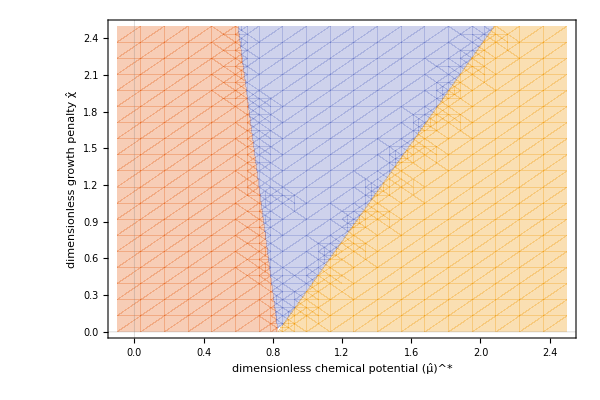

```mathematica
is= 600;
bs=17;
Jgrange=10;
μrange=8;

fext=-1;
 μ=1;
κ=1;
Clear[ps, χ];

CP=ContourPlot[{rhsLower[ps, χ, fext,μ, κ ]==0, rhsUpper[ps, χ, fext,μ, κ ]==0}//Evaluate,{ps, 0, μrange}, {χ, 0, μrange}, PlotTheme->"Scientific", BaseStyle->bs, FrameStyle->Black, ContourStyle->Black,FrameLabel->{"μ^*", "χ"}, ImageSize->is];

RP =  RegionPlot[{rhsUpper[ps, χ, fext,μ, κ ]<0, rhsLower[ps, χ, fext,μ, κ ]<0< rhsUpper[ps, χ, fext,μ, κ ], rhsLower[ps, χ, fext,μ, κ ]>0}//Evaluate,{ps, -0.1, 2.5}, {χ, 0,2.5}, PlotTheme->"Scientific", BaseStyle->bs, FrameStyle->Black,BoundaryStyle->None, FrameLabel->{"dimensionless chemical potential (μ̂)^*", "dimensionless growth  penalty χ̂"}, PlotPoints->20, ImageSize->is, AspectRatio->1/1.5]
```

```mathematica
solReduced[γ0_]:=Module[{},
First@NDSolve[{γ'[t] γ[t]^-1==ReplaceAll[RHS/.subα,γ->γ[t]],vol[t]==ReplaceAll[α^2 αz γ[t], subα], γ[0]==γ0},{γ[t], vol[t]}, {t, 0, tend}]]
```

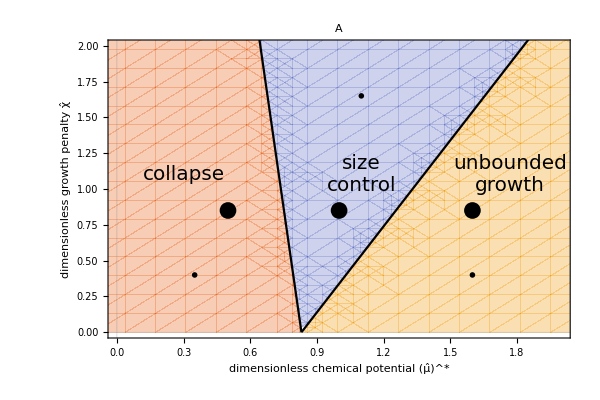

```mathematica
list={{1,0.85},{1.6,0.85},{0.5, 0.85} }; (* format: {size control,exponential,shrink} *)


bs=10;
is=130;

ps=list[[1]]//First;
χ=list[[1]]//Last;
tend=25;
PlotStable=LogPlot[vol[t]/.solReduced[#]&/@Range[0.5, 5, 0.5]//Evaluate,{t, 0, tend}, PlotRange->All, PlotTheme->"Scientific", AspectRatio->1, BaseStyle->bs, FrameStyle->Black, ImageSize->is, FrameStyle->Black, PlotStyle->Black,  FrameLabel->{"dimensionless time t̂", "scaled volume  α^2 α_z γ_z"}];

ps=list[[2]]//First;
χ=list[[2]]//Last;
PlotExp=LogPlot[vol[t]/.solReduced[#]&/@Range[1, 10, 2]//Evaluate,{t, 0, tend}, PlotRange->All, PlotTheme->"Scientific", AspectRatio->1, BaseStyle->bs, FrameStyle->Black, ImageSize->is, FrameStyle->Black, PlotStyle->Black,  FrameLabel->{"dimensionless time t̂", "scaled volume  α^2 α_z γ_z"}];

ps=list[[3]]//First;
χ=list[[3]]//Last;

PlotZero=LogPlot[vol[t]/.solReduced[#]&/@Range[1, 10, 2]//Evaluate,{t, 0, tend}, PlotRange->All, PlotTheme->"Scientific", AspectRatio->1, BaseStyle->bs, FrameStyle->Black, ImageSize->is, FrameStyle->Black, PlotStyle->Black,  FrameLabel->{"dimensionless time t̂", "scaled volume  α^2 α_z γ_z"}];

LP=ListPlot[list, PlotStyle->Directive[Black, PointSize[0.02]], PlotTheme->"Scientific"];

empty="                                                    ";
PhaseDiagram=Show[RP, CP,LP, Epilog->{Inset[PlotStable,{1.1, 1.65}], Inset[PlotExp,{1.6, 0.4}], Inset[PlotZero,{0.35, 0.4}], Inset[Style["size\ncontrol", FontFamily->"Times New Roman", FontSlant->Italic, FontSize->20],{1.1,1.1}], Inset[Style["collapse", FontFamily->"Times New Roman",  FontSlant->Italic, FontSize->20],{0.3,1.1}], Inset[Style["unbounded\ngrowth", FontFamily->"Times New Roman",  FontSlant->Italic, FontSize->20],{1.77,1.1}]}, PlotRange->{{0, 2}, {0, 2}}, PlotLabel->Style["A"<>empty<>" "<>empty, FontSize->20, FontColor->Black]]
```

### Size diagram

```mathematica
size[psP_]:=Module[{res},
ps=psP;
res=γ[t]/.solReduced[0.5]/.t->tend;
Clear[ps];
res

]
```

```mathematica
Clear@ps
InsetPlot[ps_]:=Module[{},
is=105;
bs=11;
Plot[rhsFull[Jg,ps, χ, fext,μ, κ ]//Evaluate,{Jg, 0,8}, PlotRange->{All,1.1{-1,1.3}}, ImageSize->is, BaseStyle->bs, PlotTheme->"Scientific", AspectRatio->1.4, FrameStyle->Black,  FrameLabel->{"γ_z", None},PlotStyle->Directive[Blue], PlotLegends->Placed[{"OverHat[γ̇]_zγ_z^-1"} , {Right,If[True,  Top, Bottom]}]]];

χ=1;
tend=100;
fext=-1;
 μ=1;
κ=1;
Clear[ps]
upperPsbound=ps/.First@Solve[0==rhsLower[ps, χ, fext,μ, κ ], ps]//N;
lowerPsbound=ps/.First@Solve[0==rhsUpper[ps, χ, fext,μ, κ ], ps]//N;


list={#,size[#]}&/@{1,1.7,0.5 };

InsetStable=InsetPlot[1];
InsetExp=InsetPlot[1.7];
InsetZero=InsetPlot[0.5];

RP=RegionPlot[{ps<lowerPsbound,lowerPsbound<ps<upperPsbound, ps>upperPsbound},{ps, -2, 2},{size, -1, 11}, PlotTheme->"Scientific", BoundaryStyle->None];

PP=ListPlot[{list}, PlotStyle->Directive[Black, PointSize[0.02]]];

is= 400;
bs=17;
heigthCoordinate=7.2;
data=Table[{pss,size[pss]},{pss, 0.2,1.9, 0.01}];
```

```mathematica
empty="                   ";
xshift=0.8;
LP=ListPlot[{Select[data, #[[2]]<0.2&], Select[data, #[[2]]>0.2&]}, PlotRange->{All,{-0.2, 10}}, PlotStyle->Directive[Black, Thickness[0.007]], Joined->True, PlotTheme->"Scientific", AspectRatio->1/1.2, BaseStyle->bs, ImageSize->is, FrameStyle->Black, FrameLabel->{"dimensionless chemical potential (μ̂)^*",  "scaled asymptotic size  α^2 α_z γ_z"}, Epilog->{Inset[InsetStable,{0.15+xshift, heigthCoordinate}], Inset[InsetExp,{0.82+xshift, heigthCoordinate}],  Inset[InsetZero,{-0.42+xshift,heigthCoordinate}], Inset[Style["size\ncontrol", FontFamily->"Times New Roman", FontSlant->Italic, FontSize->20],{0.15+xshift,3.5}], Inset[Style["collapse", FontFamily->"Times New Roman", FontSlant->Italic, FontSize->20],{-0.4+xshift,3.5}], Inset[Style["unbounded\ngrowth", FontFamily->"Times New Roman", FontSlant->Italic, FontSize->20],{0.8+xshift,3.5}]}, PlotLabel->Style["B"<>empty<>"present theory (χ̂ > 0)"<>empty, FontSize->20, FontColor->Black]];

SizeDiagram=Show[LP, RP, PP]
```

-Graphics-

```mathematica
χ=0;
tend=10^3;
fext=-1;
 μ=1;
κ=1;
Clear[ps]
upperPsbound=ps/.First@Solve[0==rhsLower[ps, χ, fext,μ, κ ], ps]//N;
lowerPsbound=ps/.First@Solve[0==rhsUpper[ps, χ, fext,μ, κ ], ps]//N;


list={#,size[#]}&/@{1,1.7,0.5 };

InsetStable=InsetPlot[1];
InsetExp=InsetPlot[1.1];
InsetZero=InsetPlot[0.5];

RP=RegionPlot[{ps<lowerPsbound,lowerPsbound<ps<upperPsbound, ps>upperPsbound},{ps, -2, 2},{size, -1, 11}, PlotTheme->"Scientific", BoundaryStyle->None];

PP=ListPlot[{list}, PlotStyle->Directive[Black, PointSize[0.02]]];

is= 400;
bs=17;
heigthCoordinate=7.2;
data=Table[{pss,size[pss]},{pss, 0.2,1.4, 0.01}];
```

NDSolve::ndsz: At t == 817.206, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {1000} lies outside the range of data in the interpolating function. Extrapolation will be used.

ListPlot::prng: Value of option PlotRange -> {{0.475,1.7},{-1.71554505749118×10^330,1.84844×10^73}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

```mathematica
empty="               ";
xshift=0.8; 
LP=ListPlot[{Select[data, #[[2]]<0.2&], Select[data, #[[2]]>0.2&]}, PlotRange->{All,{-0.2, 10}}, PlotStyle->Directive[Black, Thickness[0.007]], Joined->True, PlotTheme->"Scientific", AspectRatio->1/1.2, BaseStyle->bs, ImageSize->is, FrameStyle->Black, FrameLabel->{"dimensionless chemical potential (μ̂)^*",  "scaled asymptotic size  α^2 α_z γ_z"}, Epilog->{Inset[InsetExp,{1.1, heigthCoordinate}],  Inset[InsetZero,{0.5,heigthCoordinate}], Inset[Style["collapse", FontFamily->"Times New Roman", FontSlant->Italic, FontSize->20],{0.5,3.5}], Inset[Style["unbounded\ngrowth", FontFamily->"Times New Roman", FontSlant->Italic, FontSize->20],{1.1,3.5}]}, PlotLabel->Style["C"<>empty<>"classical theory (χ̂ = 0)"<>empty, FontSize->20, FontColor->Black]];

SizeDiagramClassic=Show[LP, RP, PP]
```

-Graphics-

```mathematica
Grid[{{PhaseDiagram, SpanFromLeft},{SizeDiagram, SizeDiagramClassic}}, Spacings->{4,4}]
```

-Graphics- | 
-Graphics- | -Graphics-